```mathematica
mem1=Import["~/t/log.jtotal","Text"];
mem2=Import["~/t/log2.jtotal","Text"];
```

```mathematica
itpr=Read[StringToStream@#,Number]&;
```

```mathematica
f=(itpr@#&/@StringSplit[#,"\n"])&;
mem1=f[mem1];
mem2=f[mem2];
```

```mathematica
mMem1=(#/1048576)&/@mem1;
mMem2=(#/1048576)&/@mem2;
```

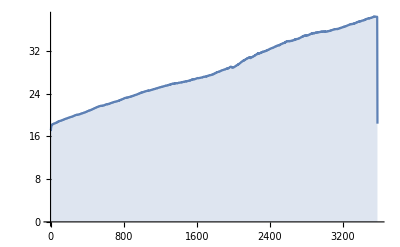

```mathematica
ListLinePlot[mMem1,Filling->Axis]
```

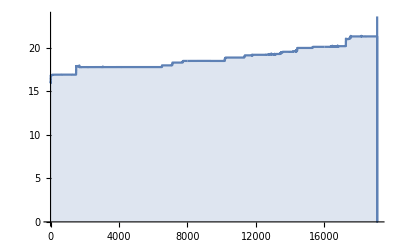

```mathematica
ListLinePlot[mMem2,Filling->Axis]
```

```mathematica
processText=((itpr/@StringSplit[#," "]&)/@StringSplit[#,"\n"])/(1048576*1024)&;
```

```mathematica
mem1Pmap=processText[Import["~/t/log.mem","Text"]];
mem2Pmap=processText[Import["~/t/log2.mem","Text"]];
```

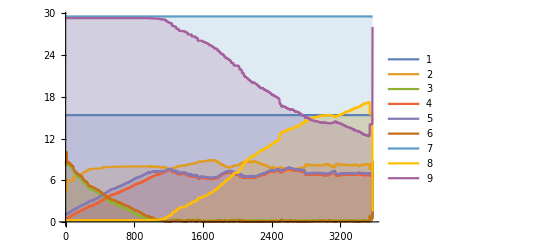

```mathematica
ListLinePlot[Table[#[[n]]&/@mem1Pmap.,{n,1,9}],Filling->Axis,PlotLegends->Automatic]
```

```mathematica
ListLinePlot[Table[#[[n]]&/@mem2Pmap,{n,1,9}],Filling->Axis,PlotLegends->Automatic]
```

-Graphics-

```mathematica
select[data_,nList_]:=Module[{list},
list={};
For[i=1,i<=Length@nList,i++,
list=Join[list,{#[[nList[[i]]]]&/@data}]
];
list
];
```

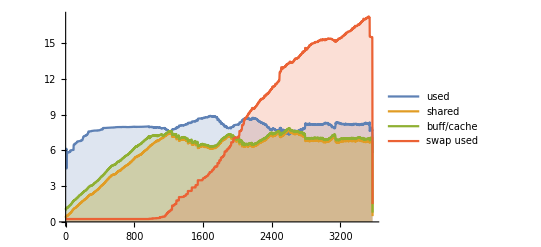

```mathematica
ListLinePlot[select[mem1Pmap,{2,4,5,8}],Filling->Axis,PlotLegends->{"used","shared","buff/cache","swap used"}]
```

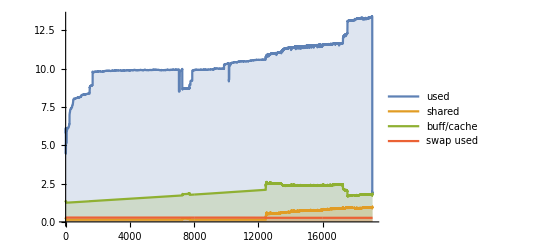

```mathematica
ListLinePlot[select[mem2Pmap,{2,4,5,8}],Filling->Axis,PlotLegends->{"used","shared","buff/cache","swap used"}]
```

```mathematica
itpr["123.456"]
```

itpr[123.456]